```mathematica
ClearAll[t1,t2,t3,t4,t5]
t1[y_]:= 5*y
t2[y_]:=81+y
t3[y_]:=57+y
t4[y_]:=6*y
t5[y_]:=13+y
```

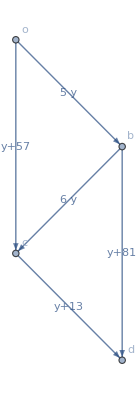

```mathematica
graph = Graph[{o->b,b->d,o->c,b->c,c->d},EdgeWeight->{t1[y],t2[y],t3[y],t4[y],t5[y]}, EdgeLabels-> "EdgeWeight", VertexLabels-> "Name"]
```

```mathematica
Ed =List@@@EdgeList[graph]
```

{{o,b},{b,d},{o,c},{b,c},{c,d}}

```mathematica
U=FindPath[graph,VertexList[graph][[1]],VertexList[graph][[3]],Infinity,All]
```

{{o,c,d},{o,b,d},{o,b,c,d}}

```mathematica
checkEd[e_]:=Table[If[MemberQ[Partition[U[[i]],2,1],e],1,0],{i,Length[U]}];
cMatrix=checkEd/@Ed
```

{{0,1,1},{0,1,0},{1,0,0},{0,0,1},{1,0,1}}

```mathematica
checkEd[e_]:=Table[If[MemberQ[Partition[U[[i]],2,1],e],1,0],{i,Length[U]}];
cMatrix=checkEd/@Ed
```

{{0,1,1},{0,1,0},{1,0,0},{0,0,1},{1,0,1}}

```mathematica
X=Transpose[{x1,x2,x3}]
```

{x1,x2,x3}

```mathematica
Xi=Table[Sum[cMatrix[[i,j]]*X[[j]],{j,Length[X]}],{i,Length[Ed]}]
```

{x2+x3,x2,x1,x3,x1+x3}

```mathematica
Talpha=Table[{t1,t2,t3,t4,t5}[[i]][Xi[[i]]],{i,Length[Xi]}]
```

{5 (x2+x3),81+x2,57+x1,6 x3,13+x1+x3}

```mathematica
T=Table[Sum[cMatrix[[i,j]]*Talpha[[i]],{i,Length[Talpha]}],{j,Length[X]}]
```

{70+2 x1+x3,81+x2+5 (x2+x3),13+x1+7 x3+5 (x2+x3)}

```mathematica
f1[x_]:=Integrate[t1[y],{y,0,x}]
f2[x_]:=Integrate[t2[y],{y,0,x}]
f3[x_]:=Integrate[t3[y],{y,0,x}]
f4[x_]:=Integrate[t4[y],{y,0,x}]
f5[x_]:=Integrate[t5[y],{y,0,x}]
```

```mathematica
f1[x]
f2[x]
f3[x]
f4[x]

f5[x]
```

{(5 x1^2)/2,(5 x2^2)/2,(5 x3^2)/2}

{81 x1+x1^2/2,81 x2+x2^2/2,81 x3+x3^2/2}

{57 x1+x1^2/2,57 x2+x2^2/2,57 x3+x3^2/2}

{3 x1^2,3 x2^2,3 x3^2}

{13 x1+x1^2/2,13 x2+x2^2/2,13 x3+x3^2/2}

```mathematica
f = {f1, f2,f3,f4,f5}
```

{f1,f2,f3,f4,f5}

```mathematica
ClearAll[x1,x2,x3]
x={x1,x2,x3};
```

```mathematica
Ffull=Total[MapThread[#1[#2]&,{f,Xi}]]
```

57 x1+x1^2/2+81 x2+x2^2/2+3 x3^2+13 (x1+x3)+1/2 (x1+x3)^2+5/2 (x2+x3)^2

```mathematica
constraints={x1+x2+x3==12,x1>=0,x2>=0,x3>=0}
Res =Minimize[{Ffull,constraints},{x1,x2,x3}]
```

{x1+x2+x3==12,x1≥0,x2≥0,x3≥0}

{-408,{x1→12,x2→0,x3→0}}

```mathematica
Res[[2,1]]
```

```mathematica
Set@@(Res[[2,1]])
Set@@(Res[[2,2]])
Set@@(Res[[2,3]])
```

25/4

0

23/4

```mathematica
x
```

{25/4,0,23/4}

```mathematica
Floor[x]
```

{6,0,5}